# Convexity in Medicine

-Graphics-
Consider a disease that is nonlinearly more lethal.
We cannot generalise benefits from the very ill to the rest of the population.
This tutorial explains simply the following.
Why most studies try to extend benefits from the extremely ill to milder symptoms?
This compares the low number needed to treat for the extremely ill.
There is a high number needed to treat for milder syndromes.

Define x = 0 as normal.

This is the payoff function.

```mathematica
f[x_]:=1/(1+Exp[4-2x])
```

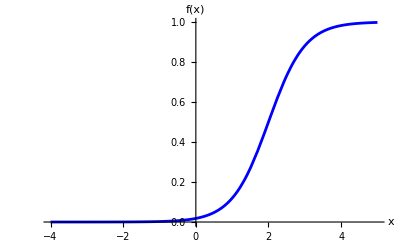

```mathematica
Plot[f[x],{x,-4,5},PlotStyle->Blue,AxesLabel->{x,"f(x)"}]
```

Start with a standard normal distribution.

```mathematica
r:=RandomVariate[NormalDistribution[0,1]]
```

Given the payoff function, take a normally distributed population and add a bit of normally distributed noise.

```mathematica
fr[x_]:=f[x] + RandomVariate[NormalDistribution[0,0.08]]
```

Run this for 400 patients. I used a larger noise than Nassim Taleb to illustrate the benefit.

```mathematica
X=Table[{x=r;x,fr[x]},{400}];
```

Plot the table. The benefits from the most vulnerable patients are apparently shifted to the middle.

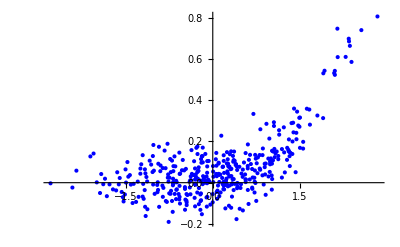

```mathematica
ListPlot[X, PlotStyle->Blue, PlotRange->All]
```